```mathematica
Remove["Global`*"]
```

```mathematica
DirichletBCs[f_,x_,xm_]:=f-((((f/.x->-xm)-(f/.x->xm))/2)(Cos[(x+xm)/(2xm)Pi]+1)+(f/.x->xm))
```

```mathematica
DirichletBCs[Exp[-x^2],x,xm]/.x->xm
```

0

```mathematica
DirichletBCs[Exp[-x^2],x,xm]/.x->-xm
```

0

```mathematica
SchrodingerEq=I D[ψ[t,x],t]==-(1/2)D[ψ[t,x],x,x]+6 Exp[-x^2]ψ[t,x]
```

ⅈ ψ^(1,0)[t,x]==6 ⅇ^(-x^2) ψ[t,x]-1/2 ψ^(0,2)[t,x]

```mathematica
xm:=15
T:=5
```

```mathematica
DSolve[SchrodingerEq,{ψ},{t,x}]
```

DSolve[ⅈ ψ^(1,0)[t,x]==6 ⅇ^(-x^2) ψ[t,x]-1/2 ψ^(0,2)[t,x],{ψ},{t,x}]

```mathematica
sol:=NDSolve[{SchrodingerEq,ψ[0,x]==DirichletBCs[Exp[-(x+3)^2],x,xm]Exp[3I x],ψ[t,-xm]==0,ψ[t,xm]==0},{ψ[t,x]},{t,0,T},{x,-xm,xm},AccuracyGoal->3,PrecisionGoal->3]
```

```mathematica
(*ByteCount[sol]/10.^6*)
```

```mathematica
Plot3D[Evaluate[Abs[ψ[t,x]]/.sol],{t,0,T},{x,-xm,xm}, PlotRange->All]
```

-Graphics3D-

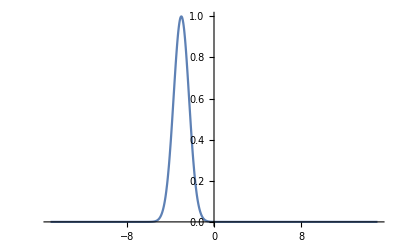

```mathematica
Plot[ Evaluate[Abs[ψ[t,x]/.sol]/.t->0],{x,-xm,xm},PlotRange->All]
```

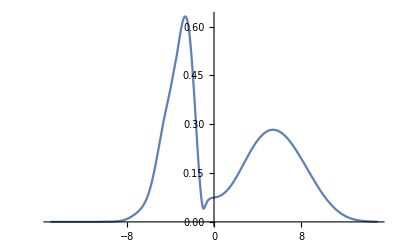

```mathematica
Plot[ Evaluate[Abs[ψ[t,x]/.sol]/.t->2.5],{x,-xm,xm},PlotRange->All]
```

```mathematica
Manipulate[Plot[ {Evaluate[Abs[ψ[t,x]/.sol/.t->s]]},{x,-xm,xm},PlotRange->All] ,{s,0,T}]
```